# Report Project 2

Course code: IX1500
Date: 2020-09-24

Simon Johannesson, sijohann@kth.se
William Asp, wasp@kth.se

## Project 2: RSA cryptography

## Summary

### Task

#### Task 1

The task consisted of decrypting a message encrypted with RSA, by cracking an RSA key.

#### Task 2

The problem is to write a method that will crack a cipher that is encrypted with an RSA key. Then use that same method to determine how long time it takes to crack ciphers with RSA keys with public modulus values that are between 100 and 200 bits long.

A model should be derived from the data and then predictions should be made for how long time it would take to crack ciphers that have n-values that are 1024, 2048 and 4096 bits long.

### Result

#### Task 1

RSA key was cracked. The message that was decrypted was:

"Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue the requirements for a higher grade you need to solve one more problem. The quote you should encrypt and crack is: 'Simplicity is a great virtue but it requires hard work to achieve it and education to appreciate it. And to make matters worse: complexity sells better. By Edsger W. Djikstra'           "

#### Task 2

Times to crack RSA keys are exponential to the to it’s n-values bit length.

Approximated time to crack RSA key with n-value with bit length 1024:  7.95362×10^21   years
Approximated time to crack RSA key with n-value with bit length 2048:  1.67059×10^56   years
Approximated time to crack RSA key with n-value with bit length 4096:  7.37027×10^124  years

The approximation is based on an individual computers performance.

## Calculations

### Equations

#### Task 1

For Bob to decrypt, he needs to follow the below specification: 
n_Bob>n_Alice⇒c_1≡_n_Bob c_Alice^d_Bob, m_Alice≡_n_Alice c_1^e_Alice
n_Alice>n_Bob⇒c_1≡_n_Alice c_Alice^e_Alice, m_Alice≡_n_Bob c_1^d_Bob
So the first step is to determine which statement is true
n_Bob>n_Alice  
or
n_Alice>n_Bob

Since 
 n_Bob>n_Alice = True
 The decryption to the value m should follow:
 c_1≡_n_Bob c_Alice^d_Bob,
 m_Alice≡_n_Alice c_1^e_Alice
 But the Bob’s d value is not known.
 
 It can however be calculated, because: 
 n = p q, (p , q) ∈ ℙ, ℙ is the set of all prime numbers 
ϕ = (p-1)(q-1)
d = e^-1 mod ϕ

Now that the d value has been determined, the decryption can be performed.

#### Task 2

First step is to create the functions needed to encode the message string.

Then create an encrypt function that follows the specification below to encrypt m and returns cipher cipher: 
m_Alice<n_Bob
c_Alice≡_n_Bob m_Alice^e_Bob

Create a decryption function that follows the specification for decryption : 
m_Alice≡_n_Bob c_Alice^d_Bob

Decoding the m values

To decrypt a message encrypted with RSA it is necessary to know the private key value d, and the public key value n. The d value can be calculated 
n = p q, (p , q) ∈ ℙ, ℙ is the set of all prime numbers 
ϕ = (p-1)(q-1)
d = e^-1 mod ϕ

### Discussion

#### Task 1

With an understanding of the RSA encryption and decryption protocol/specification it is trivial to understand how an RSA key is cracked. Doing it by hand would be difficult but a normal personal computer could easily crack the key in the task. Since the message in the task was split up in smaller sections, to be able to be encrypted by the short key, the encryption had to be performed several times with different ciphers, but the same keys, and then combined at a later stage. This was observed to be a clever way to encrypt messages that are really too long for the key.

#### Task 2

It became clear from the results that it is not practically possible to crack RSA keys, if the keys use n-values with large bit lengths. The limiting factor is that it is incredibly CPU intensive to factor numbers that are products of two large prime numbers.

Since time is a limiting factor when cracking the keys only a few tests were run, so the data that was used to derive a model was suboptimal. The reason is that the RSA keys were somewhat randomly generated which may have caused the crack times to not display in a way that might have been expected, a perfect exponential curve. Two ways could have been used to mitigate that issue. The first is to not generate the RSA keys randomly. However, it was believed that it could cause unforeseen disturbances with the internals of the function FactorInteger of which nothing was known. The second way is to run the tests several times and calculate averages or medians of the times and thus smoothen out the curve. It was however determined to be far too time consuming in comparison to the value it would provide for this task. The data shows a clear trend but the model will be of poor precision.

### Diagrams

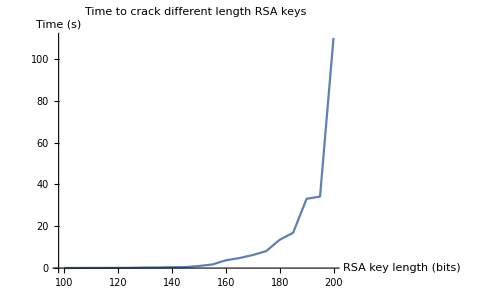

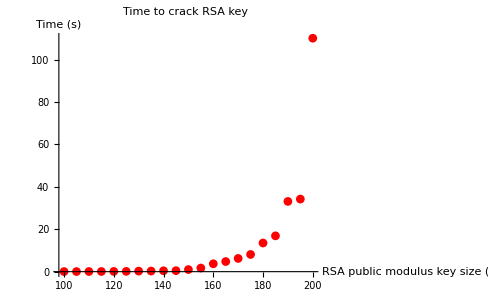

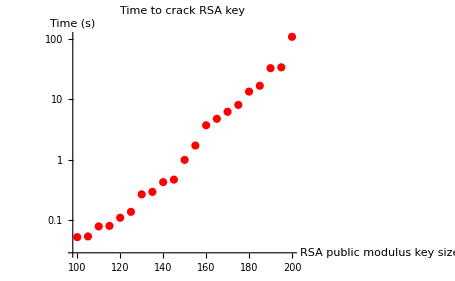

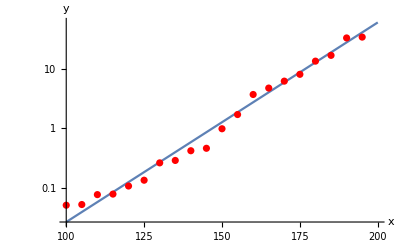

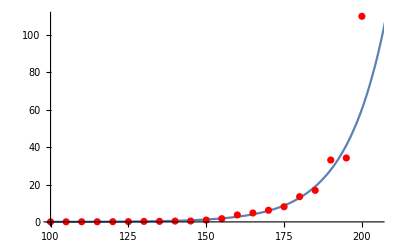

### Conclusion

Empty

#### Task 1

RSA keys with n-values consisting of the product of small p and q values are easily and quickly cracked.

#### Task 2

Although the model that was chosen is considered to have very poor precision it is clear that it is practically impossible, with the technology available today, to crack RSA keys with high n-values. To derive a model from the data is very practical when data that cannot be produced/generated, such as how long time would it take to decrypt a very long RSA key, in any reasonable way.

## Code

### Task 1

#### Initializing values

Professor Alice har skickat en uplift till Bob, en av hennes studenter. För att säkerställa att uppgiften verkligen kommer från henne så signerar hon meddelandet med hjälp av metoden i avsnitt 2.2.6 ovan. Du skall lösa problemet, men då måste du börja med att knäcka kryptot som skickats till Bob. Använd basen 256 när du översätter till ASCII-kod.

```mathematica
nAlice=173067809568650650254651948453757071454112069885961677;
eAlice=3287;
nBob=685746563565213593998991828025682278267914215114717399;
eBob=4141;
cipher={
531301545192540526538562996119874005598394953581889980,253835033608045670746495776870704267971322752833501069,295494800605225121649532827884904960119794411935318191,356889556103931306723253587635046687635524222913958813,665170545927968575573343996326340876350432556729975135,469306660346680678018973492642493227583506074572127129,669864849052286592977992159216572272286187322129900601,67443874762881965068907073487271177009837307742146186,206963942810038249337504906086720011644974589155509486,12361993292067904922905562651618411716312523967763152,596105513854241524904599343954988876751152556443182365,118957298362710351312498532203563871421459266333348755,439001139546986502255653331254032172395219069204122787,34270241039450294802362132705578076084635135877988959,627063000861103394259253981356349035768721801641804458,634987884160816833480771068222516460351076121185551581,398172872629132780981103160396970382112041774336326577,381781261026724515120629160669181445588834230492536128,164633715063442543263858143455229965317936486655924024,552098460217762425462814236077839572074083170864774859,683958399609386999975662847975279796030167103223715834,263312158667004158391146985765292815817678708765542785};
```

#### Solution

For Bob to decrypt, he needs to follow the below specification: 
n_Bob>n_Alice⇒c_1≡_n_Bob c_Alice^d_Bob, m_Alice≡_n_Alice c_1^e_Alice
n_Alice>n_Bob⇒c_1≡_n_Alice c_Alice^e_Alice, m_Alice≡_n_Bob c_1^d_Bob
So the first determine which statement is true
n_Bob>n_Alice  
or
n_Alice>n_Bob

```mathematica
nBob>nAlice
```

True

Since 
 n_Bob>n_Alice = True
 The decryption to the value m should follow:
 c_1≡_n_Bob c_Alice^d_Bob,
 m_Alice≡_n_Alice c_1^e_Alice
 But the Bob’s d value is not known.
 
 It can however be calculated, because: 
 n = p q, (p , q) ∈ ℙ, ℙ is the set of all prime numbers 
ϕ = (p-1)(q-1)
d = e^-1 mod ϕ

```mathematica
{pBob,qBob}=FactorInteger[nBob][[All,1]];
ϕBob=(pBob-1)(qBob-1);
dBob=PowerMod[eBob,-1,ϕBob];
```

Now that the d value has been determined, the decryption can be performed.

```mathematica
c1=PowerMod[cipher,dBob,nBob];
mFromAlice=PowerMod[c1,eAlice,nAlice];
```

The value m was encoded from ascii letters to a number by Alice, so it must be decoded back to ascii letters. The base 256 was used.

```mathematica
B= 256;
ascii={};
For[i=1,i≤Length[mFromAlice],i++,
q=mFromAlice[[i]]; 
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
]
FromCharacterCode[ascii];
msg=FromCharacterCode[ascii]
```

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue the requirements for a higher grade you need to solve one more problem. The quote you should encrypt and crack is: 'Simplicity is a great virtue but it requires hard work to achieve it and education to appreciate it. And to make matters worse: complexity sells better. By Edsger W. Djikstra'

### Task 2

#### Initializing values

```mathematica
Clear["`*"];
```

Skriv en metod RSAcrack[cipher,n,e] som knäcker ett standard RSA krypto och returnerar klartext från en matris av krypterade tal. Undersök sedan hur lång tid det tar att knäcka kryptot av meddelandet från uppgiften ovan med olika storlekar på nyckeln n (100-200 bits). Visualisera resultet i en graf. Läs sedan noggrant avsnitt 2.3 ovan och anpassa en modell till de data ni har fått fram. Använd modellen för att förutsäga hur lång tid det skulle ta att knäcka ett skiffer där n är 1024 bit, 2048 bit eller 4096 bit lång.

```mathematica
message ="Simplicity is a great virtue but it requires hard work to achieve it and education to appreciate it. And to make matters worse: complexity sells better. By Edsger W. Djikstra";
```

#### Encryption helper functions

First step is to create the functions needed to encode the message string.

```mathematica
(* takes a message string and a base, encodes and returns m *)
messageToM[message_,base_]:=ToCharacterCode[message].base^(Range[StringLength[message]]-1)
```

Then create an encrypt function that follows the specification below to encrypt m and returns cipher cipher: 
m_Alice<n_Bob
c_Alice≡_n_Bob m_Alice^e_Bob

```mathematica
(* encrypts m with receivers public key values e and n, return c *)
singleEncrypt[m_, eRec_,nRec_]:=PowerMod[m, eRec, nRec]
```

#### Decryption helper functions

Create a decryption function that follows the specification for decryption : 
m_Alice≡_n_Bob c_Alice^d_Bob

```mathematica
(* decrypts c with receivers key values d and n, return m *)
singleDecrypt[c_, dRec_, nRec_]:=PowerMod[c, dRec, nRec]
```

```mathematica
(* decrypts a list of c, return a list of m *)
singleDecryptAll[cSenList_, nRec_,dRec_]:=
Map[singleDecrypt[#, dRec, nRec]&, cSenList];
```

Decoding the m values

```mathematica
(* decode the message number into a string *)
mToMessage[m_, base_]:= Module[{q, ascii},
q = m;
ascii = {};
While[q≠ 0,
AppendTo[ascii, Mod[q,base]];
q=Quotient[q,base];
];
FromCharacterCode[ascii]
]
(* decode a list of message numbers into a string *)
allMToMessage[numList_, base_]:=
StringJoin[ Map[mToMessage[#, base]&, numList]]
```

#### Cracking helper functions

To decrypt a message encrypted with RSA it is necessary to know the private key value d, and the public key value n. The d value can be calculated 
n = p q, (p , q) ∈ ℙ, ℙ is the set of all prime numbers 
ϕ = (p-1)(q-1)
d = e^-1 mod ϕ

```mathematica
(* returns {p,q} *)
genPQ[n_]:= FactorInteger[n][[All, 1]]
(* takes {p, q}, returns ϕ *)
genϕ[{p_, q_}]:=(p -1)(q-1)
(* calculates d value, takes e and ϕ values, returns d *)
genD[E_, ϕ_]:= PowerMod[E, -1,ϕ]
(* cracks d, takes the public key values n and e *)
crackD[n_,e_]:=genD[e, genϕ[genPQ[n]]]
```

#### Automatic generation of RSA key values functions

In order to perform tests it is necessary to be able to generate RSA key values automatically, dependant on the wanted bit length of the n value.

```mathematica
(* generates random p and q, p*q has a high chance to be of the decided bit length, 
it may be necessary to run several times in order to receive 
the wanted output,
returns {{p, q}, BitLength[p*q]} *)
randomPandQ[bitLenOfProduct_]:= Module[
{p, q, min, max,bitLenP, bitLenQ, xorNum},
min=IntegerPart[bitLenOfProduct/2 -1];
max=IntegerPart[bitLenOfProduct/2 +1];
p= NextPrime[RandomInteger[{2^min, 2^max}]];
bitLenP = BitLength[p];
bitLenQ =bitLenOfProduct-bitLenP;
xorNum = RandomInteger[{2^(bitLenQ-5), 2^(bitLenQ-1)}];
q=NextPrime[BitXor[2^bitLenQ,xorNum]];
{{p, q}, BitLength[p*q]}
]
(* generates random RSA numbers, n has the bit length of bitLenOfN,
returns {p, q, n, ϕ, e, d} *)
randomRSAnums[bitLenOfN_]:= Module[
{p,q, bLen, n,rnd,ϕ,e,d},
{{p,q},bLen}=randomPandQ[bitLenOfN];
While[bLen≠bitLenOfN,
{{p,q},bLen}=randomPandQ[bitLenOfN];
];
n=p*q;
ϕ=(p-1)(q-1);
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[e=rnd,ϕ]≠ 1];
d=PowerMod[e, -1, ϕ];
{p,q,n,ϕ,e,d}
]
```

#### Encryption functions

```mathematica
(* encrypts a string message with the receivers values e and n,
returns a list of ciphers, c *)
singleEncryptFromString[message_, eRec_,nRec_ ,base_]:=Module[
{j,k,messLen,ptMessage,encryptedList , cond,m},
encryptedList = {};
cond = True;
j= 1;
k= 1;
messLen = StringLength[message];
While[j ≤ messLen,

While[ cond,
ptMessage = StringJoin[StringPart[message, j;;k;;1]];
m=messageToM[ptMessage,base];

If[m ≥ nRec,
k--;
cond=False;
ptMessage=StringJoin[StringPart[message, j;;k;;1]];
m = messageToM[ptMessage,base];
,
If[ k ≥ messLen,
cond=False; 
,
k++;
];
];
];

AppendTo[encryptedList,singleEncrypt[m, eRec,nRec]];

If[k ≤ messLen ,
cond=True;
j = k+1;
k=j;
];
];
encryptedList
]
```

#### Decryption functions

```mathematica
(* decrypts list of ciphers with receivers n and d values,
returns a string of message *)
singleDecryptToString[cipherList_, nRec_,dRec_, base_]:=
allMToMessage[singleDecryptAll[cipherList, nRec,dRec],base]
```

#### Cracking function

```mathematica
(* cracks a cipher list and returns the message,
 arguments: 
cipher list, 
 public n value, 
 public e value *)
RSAcrack[cipherList_,n_,e_]:= 
singleDecryptToString[cipherList, n, crackD[n,e], 256]
```

#### Timing function

```mathematica
(* takes the time to crack a given message encrypted with an RSA key
  with different bit length of n.
  
 automatically creates RSA keys for sender and receiver,
   automatically encrypts a message,
   automatically cracks the encryption (and decrypts the message),
   automatically takes the time for cracking the encryption,
   returns {list of bit lenghts tested, times to crack encryption}
    *)
RSAcrackTiming[message_, minBitLength_, maxBitLength_, increment_]:=Module[
{base, bitLenList, timesList, bitLen, pSen,qSen,nSen,ϕSen,eSen, dSen,pRec,qRec,nRec,ϕRec,eRec, dRec, c , crackedMessage},
base =256;
bitLenList = {};
timesList = {};
For[bitLen = minBitLength, bitLen≤ maxBitLength, bitLen += increment,
{pSen,qSen,nSen,ϕSen,eSen, dSen}=randomRSAnums[bitLen];
{pRec,qRec,nRec,ϕRec,eRec, dRec}=randomRSAnums[bitLen];
c = singleEncryptFromString[message, eRec,nRec ,base];
AppendTo[bitLenList, bitLen];
AppendTo[timesList, AbsoluteTiming[crackedMessage = RSAcrack[c, nRec, eRec]][[1]]];
Print["Decrypted key with bit length: ", bitLen];
(* Print["Decrypted message: ", crackedMessage]; *)
];
{bitLenList, timesList}
]
```

#### Taking the times

Decrypted key with bit length: 100

Decrypted key with bit length: 105

Decrypted key with bit length: 110

Decrypted key with bit length: 115

Decrypted key with bit length: 120

Decrypted key with bit length: 125

Decrypted key with bit length: 130

Decrypted key with bit length: 135

Decrypted key with bit length: 140

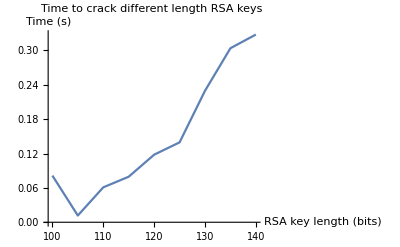

```mathematica
(* Example code *)
timeDataSmall = RSAcrackTiming[message, 100, 140, 5];
dataSmall = Transpose[timeDataSmall];
ListLinePlot[dataSmall,
PlotLabel->"Time to crack different length RSA keys",
AxesLabel-> {"RSA key length (bits)","Time (s)"},
PlotRange->Full
]
```

```mathematica
data = {{100,0.051393},{105,0.052793},{110,0.077445},{115,0.07904},{120,0.107998},{125,0.135188},{130,0.264322},{135,0.290357},{140,0.422595},{145,0.464552},{150,0.988578},{155,1.713563},{160,3.72046},{165,4.769045},{170,6.235202},{175,8.115938},{180,13.510855},{185,16.892628},{190,33.129527},{195,34.235115},{200,110.100646}};
ListLinePlot[data,
PlotLabel->"Time to crack different length RSA keys",
AxesLabel-> {"RSA key length (bits)","Time (s)"},
PlotRange->Full
]
```

-Graphics-

#### Determining an appropriate model

The dataset below contains the calculations of the time to crack a cipher of different bit sizes of n. The left value is The bit size, and the right value is the time to crack the cipher.

```mathematica
data={{100,0.051393},{105,0.052793},{110,0.077445},{115,0.07904},{120,0.107998},{125,0.135188},{130,0.264322},{135,0.290357},{140,0.422595},{145,0.464552},{150,0.988578},{155,1.713563},{160,3.72046},{165,4.769045},{170,6.235202},{175,8.115938},{180,13.510855},{185,16.892628},{190,33.129527},{195,34.235115},{200,110.100646}};
```

Let’s split the data so it is easier to work with.
The bit sizes of n:

```mathematica
𝕩=data[[All,1]]
```

{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200}

The times to crack the cipher:

```mathematica
𝕪=data[[All,2]]
```

{0.051393,0.052793,0.077445,0.07904,0.107998,0.135188,0.264322,0.290357,0.422595,0.464552,0.988578,1.71356,3.72046,4.76905,6.2352,8.11594,13.5109,16.8926,33.1295,34.2351,110.101}

Let’s plot the data so we see what we’re working with.

```mathematica
dataplot=ListPlot[data,PlotRange->Full,
PlotStyle->Red,
PlotLabel->"Time to crack RSA key",
AxesLabel->{"RSA public modulus key size (bits)","Time (s)"}]
```

-Graphics-

From the dataplot, we believe the data to grow exponentially. If it is exponential the data should give a straight line in a semi-log plot (lin-log plot) in which the x-axis is linear and the y-axis is logarithmic. The scale on the y-axis is chosen using the inverse function y=e^x⇔ln(y)=x.

y=c e^(a x)⇔ln(y)=ln(c)+k x⇔ln(y)=a x+b⇔y=e^(a x+b)

```mathematica
datalogplot=ListLogPlot[data,PlotStyle->Red,
PlotLabel->"Time to crack RSA key",
AxesLabel->{"RSA public modulus key size (bits)","Time (s)"}]
```

-Graphics-

Here we see that the data fits pretty good as an exponential function, since the data is in a pretty straight line.

If the data fits a straight line in a log(y)-lin(x) plot, then the model is an exponential function. We want to fit a model to our data, and to do that we need to perform the log operation on the Y values, to be able to fit our model to the data in a straight line.

```mathematica
dataWithLog=Transpose[{𝕩,Log[𝕪]}]
```

{{100,-2.96825},{105,-2.94138},{110,-2.55819},{115,-2.5378},{120,-2.22564},{125,-2.00109},{130,-1.33059},{135,-1.23664},{140,-0.861341},{145,-0.766682},{150,-0.0114877},{155,0.538575},{160,1.31385},{165,1.56215},{170,1.83021},{175,2.09383},{180,2.60349},{185,2.82688},{190,3.50042},{195,3.53325},{200,4.70139}}

Find a fitting model to the data. Find the best values for a and b to make a linear function that fits our dataWithLog.

```mathematica
solution=FindFit[dataWithLog,a x+b,{a,b},x]
```

{a→0.0771778,b→-11.3355}

The linear function should now fit our dataWithLog.
We plug the a and b values into a function that will output a predicted y value based on the x value.

```mathematica
y[x_]=ⅇ^(a x+b)/.solution
```

ⅇ^(-11.3355+0.0771778 x)

Let’s see if the model fits out data.

```mathematica
modelplot=LogPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

-Graphics-

Yes we think that the model fits our data!
Let’s see how it fits in a normal x and y coordinate system, without the log on the data or coordinate system.

```mathematica
model=Plot[y[x],{x,100,250},PlotRange->All];
Show[model,dataplot,PlotRange->{{100,205},{0,110}}]
```

-Graphics-

The model is deemed to be satisfactory, with that model it will be possible to approximate how long time it will take to crack ciphers that would take too long to actually take the time of.

#### Approximating time needed to crack a RSA key with an n-value 1024, 2048 and 4096 bits long

Cracking a cipher of 1024 bits:

```mathematica
y[1024]
```

2.50825×10^29

The result we get here is in seconds, lets find out how many years that is!

```mathematica
secondsToYears[seconds_]:=seconds/60/60/24/365
```

```mathematica
secondsToYears[y[1024]]
```

7.95362×10^21

After such a long time, anything that is decrypted is most unlikely to be of value to anyone.
For the bigger numbers:

```mathematica
secondsToYears[y[2048]]
```

1.67059×10^56

```mathematica
secondsToYears[y[4096]]
```

7.37027×10^124